## Non-discrete calculation of E-field

### Here we turn the electric potential values for a 1x1 cube we have into electric field values

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Lara\Documents\Physics\Witten\Electrophoreses\Electrophoresis

For comparison, here is the discrete field we calculated

```mathematica
SetDirectory["C:\\Users\\Lara\\Documents\\Physics\\Witten\\Electrophoreses\\Electrophoresis\\"]
<<smallDenseCubeFieldFinal.mx
```

C:\Users\Lara\Documents\Physics\Witten\Electrophoreses\Electrophoresis

```mathematica
Ezero = {2/3,0,0}
```

{2/3,0,0}

```mathematica
EzeroTable = Table[Flatten[Ezero], length];
```

```mathematica
EField[r_] := Sum[If[r ==newSides[[j]], 2Pi/density[j]*normal[newSides[[j]]]*Q[[j]], R[r, j]*Q[[j]]], {j,length}]+Ezero
```

```mathematica
R1[r_,j_]:=1/(Norm[r- newSides[[j]]])
```

```mathematica
normalOfField=Table[EzeroTable[[i]].normal[newSides[[i]]], {i, length}];
Q= LinearSolve[EMatrix, normalOfField];
```

The discrete potential:

```mathematica
Potential[r_] := Sum[If[r ==newSides[[j]], 2Pi*(Sqrt[density[j]/Pi])/density[j]*Q1[[j]], R1[r, j]*Q1[[j]]], {j,length}]+ 2/3*r[[1]]
```

Because the box we used discrete data on did not have the same dimensions as the one from the non-discrete data, we have to make sure to account for the difference in dimensions when we compare the data by multiplying the results by the half side length of one of the data sets divided by the half sidelength of the other

```mathematica
BoundingRegion[boxCentered]
```

Cuboid[{-0.4,-0.43301,-0.433015},{0.4,0.43301,0.433015}]

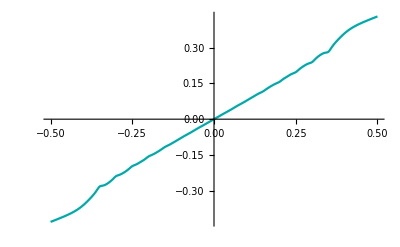

```mathematica
Plot[Potential[{x, 0.43301,0.01}], {x, -.5,.5}, PlotStyle->Darker[Cyan]]
```

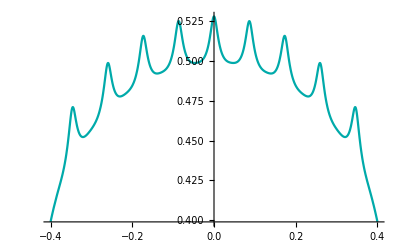

```mathematica
Plot[Potential[{0.4,x,0.01}], {x, -.4,.4}, PlotStyle->Darker[Cyan]]
```

```mathematica
sidedata = Import["cube_potential_side.txt", "Table"];
```

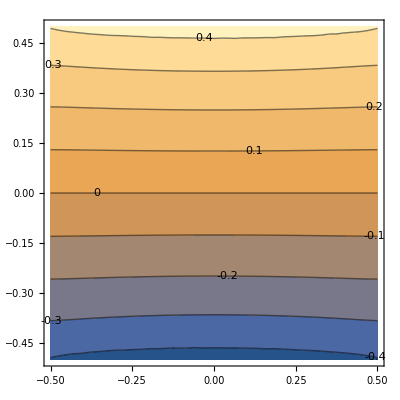

```mathematica
ListContourPlot[sidedata, ContourLabels->All]
```

```mathematica
topdata = Import["cube_potential_top.txt", "Table"];
```

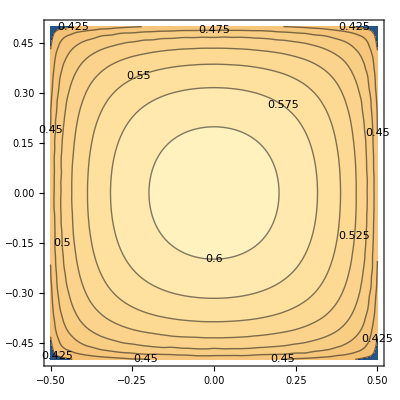

```mathematica
ListContourPlot[topdata, ContourLabels->All]
```

## Construct E fields

### We interpolated the potential at each point form the known data points:

```mathematica
topdata[[1]]
```

{-0.5,-0.5,0.405716000000000021}

```mathematica
sideFunction=Interpolation[{{#[[1]], #[[2]]},#[[3]]}&/@sidedata]
```

InterpolatingFunction[…]

```mathematica
topfunction=Interpolation[{{#[[1]], #[[2]]},#[[3]]}&/@topdata]
```

InterpolatingFunction[…]

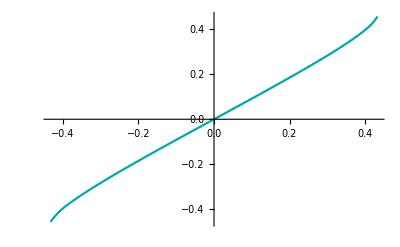

```mathematica
Plot[sideFunction[.01*.5/0.43301, z*.5/0.43301], {z, -.43301,.43301}, PlotStyle->Darker[Cyan]]
```

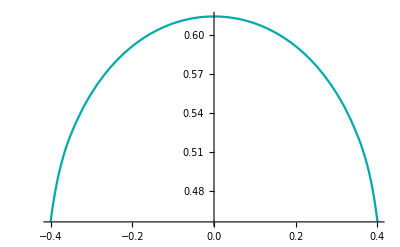

```mathematica
Plot[topfunction[x*.5/0.4, 0.01*.5/0.4], {x, -.4,.4}, PlotStyle->Darker[Cyan]]
```

Comparing the potentials

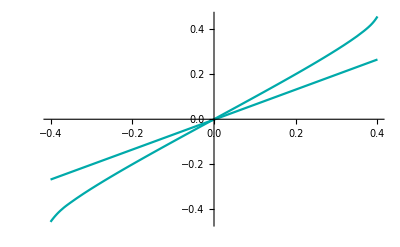

```mathematica
Plot[{Potential[{x, 0.43301,0.01}],sideFunction[.01*.5/0.4, x*.5/0.4]}, {x, -.4,.4}, PlotStyle->Darker[Cyan]]
```

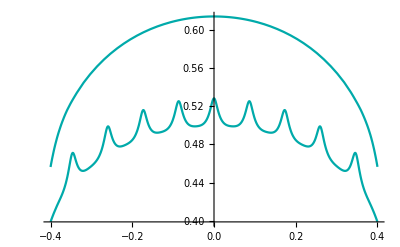

```mathematica
Plot[{Potential[{0.4,x,0.01}],topfunction[x*.5/0.4, 0.01*.5/0.4]}, {x, -.4,.4}, PlotStyle->Darker[Cyan]]
```

```mathematica
topcontoursG = ContourPlot[topfunction[x, y], {x, -.5, .5}, {y, -.5, .5}, ContourLabels->All]
```

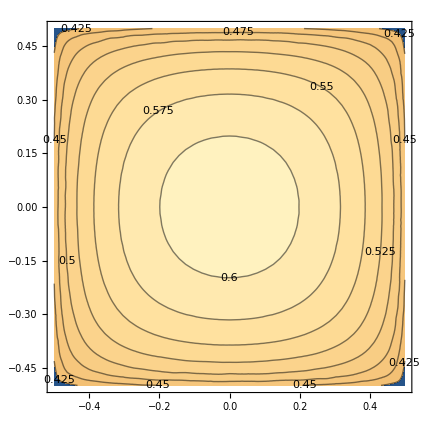

```mathematica
BoundingRegion[boxCentered]
```

Cuboid[{-0.4,-0.43301,-0.433015},{0.4,0.43301,0.433015}]

Finding E - field from the non-discrete data

```mathematica
efieldTop[u_, v_] = D[topfunction[x*.5/.43301, y*.5/.43301], {{x, y}}]/.{x->u, y->v}
efieldSideXZ[u_, v_] = D[sideFunction[z*.5/.433015, x*.5/.4], {{z, x}}]/.{x->u, z->v}
efieldSideXY[u_, v_] = D[sideFunction[y*.5/.43301, x*.5/.4], {{y, x}}]/.{x->u, y->v}
```

{1.15471 InterpolatingFunction[…][1.15471 u,1.15471 v],1.15471 InterpolatingFunction[…][1.15471 u,1.15471 v]}

{1.15469 InterpolatingFunction[…][1.15469 v,1.25 u],1.25 InterpolatingFunction[…][1.15469 v,1.25 u]}

{1.15471 InterpolatingFunction[…][1.15471 v,1.25 u],1.25 InterpolatingFunction[…][1.15471 v,1.25 u]}

```mathematica
EfieldXZ[r_] :=  {efieldSideXY[r[[1]],r[[3]]][[2]], 0, efieldSideXY[r[[1]],r[[3]]][[1]]}
EfieldXY[r_] :=  {efieldSideXZ[r[[1]],r[[2]]][[2]], efieldSideXZ[r[[1]],r[[2]]][[1]], 0}
EfieldBottom[r_] := Join[{0},efieldTop[r[[2]],r[[3]]]]
EfieldTop[r_] := Join[{0},-efieldTop[r[[2]],r[[3]]]]
```

```mathematica
EfieldKoolstra[r_]:= If[r[[1]] == .4 , EfieldBottom[r], If[ r[[1]] == -.4, EfieldTop[r], If[Abs[r[[2]]] == 0.43301, EfieldXZ[r], If[Abs[r[[3]]]==0.4330154637336504, EfieldXY[r], Null]]]]
```

```mathematica
SetDirectory[NotebookDirectory[]]
DumpSave["KoolstraEfield.mx", "Global`"]
```

C:\Users\Lara\Documents\Physics\Witten\Electrophoreses\Electrophoresis

{Global`}